```mathematica
(*First we curve-fit Pfail as a function of p and L, in accordance with (A1) of Watson and Barrett (2014)*)
SetDirectory[NotebookDirectory[]];
s=Import["results_ToricOdd.xlsx"][[1]];
sNames=s[[1]]
sData=s[[2;;]]
sData[[;;,1]]
```

{p,L,I,varI}

{{0.01,3.,0.00607114,1.66×10^-8},{0.01,5.,0.00101372,2.17×10^-9},{0.01,7.,0.000126092,2.34×10^-10},{0.01,9.,0.0000296,5.37×10^-11},{0.01,11.,2.86×10^-6,},{0.02,3.,0.0194696,4.23×10^-8},{0.02,5.,0.00683277,1.28×10^-8},{0.02,7.,0.00277565,3.23×10^-9},{0.02,9.,0.000540757,7.34×10^-10},{0.02,11.,0.000100915,1.64×10^-10},{0.03,3.,0.0370544,6.7×10^-8},{0.03,5.,0.020907,3.19×10^-8},{0.03,7.,0.0121366,1.33×10^-8},{0.03,9.,0.00501285,5.03×10^-9},{0.03,11.,0.00151189,1.81×10^-9},{0.04,3.,0.0573045,8.69×10^-8},{0.04,5.,0.0411101,5.65×10^-8},{0.04,7.,0.0392878,3.2×10^-8},{0.04,9.,0.0227223,1.72×10^-8},{0.04,11.,0.00977385,},{0.05,3.,0.07725,9.95×10^-8},{0.05,5.,0.0580166,8.36×10^-8},{0.05,7.,0.114961,5.57×10^-8},{0.05,9.,0.0681931,3.88×10^-8},{0.05,11.,0.0381862,},{0.06,3.,0.0953875,1.04×10^-7},{0.06,5.,0.065912,1.12×10^-7},{0.06,7.,0.21547,7.77×10^-8},{0.06,9.,0.154268,},{0.06,11.,0.106037,}}

{0.01,0.01,0.01,0.01,0.01,0.02,0.02,0.02,0.02,0.02,0.03,0.03,0.03,0.03,0.03,0.04,0.04,0.04,0.04,0.04,0.05,0.05,0.05,0.05,0.05,0.06,0.06,0.06,0.06,0.06}

{{{3.,0.006070.00026},{5.,0.001010.00009},{7.,0.0001260.000031},{9.,0.0000300.000015},{11.,2.86×10^-62 √}},{{3.,0.01950.0004},{5.,0.006830.00023},{7.,0.002780.00011},{9.,0.000540.00005},{11.,0.0001010.000026}},{{3.,0.03710.0005},{5.,0.02090.0004},{7.,0.012140.00023},{9.,0.005010.00014},{11.,0.001510.00009}},{{3.,0.05730.0006},{5.,0.04110.0005},{7.,0.03930.0004},{9.,0.022720.00026},{11.,0.009773852 √}},{{3.,0.07730.0006},{5.,0.05800.0006},{7.,0.11500.0005},{9.,0.06820.0004},{11.,0.03818622 √}},{{3.,0.09540.0006},{5.,0.06590.0007},{7.,0.21550.0006},{9.,0.1542682 √},{11.,0.1060372 √}}}

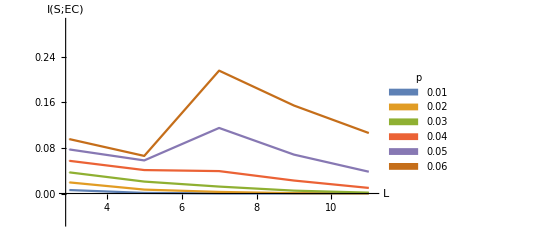

results_Odd.pdf

```mathematica
Transpose[{sData[[;;,3]],2*Sqrt[sData[[;;,3]]]}];
Data=Apply[Around,Transpose[{sData[[;;,3]],2*Sqrt[sData[[;;,4]]]}],1];
DataPlot=Partition[Transpose[{sData[[;;,2]],Data}],5]
plot=ListLinePlot[DataPlot,AxesLabel->{"L","I(S;EC)"},PlotRange->{{2.9,11.1},{-0.05,0.3}},PlotLegends->Placed[SwatchLegend[DeleteDuplicates[sData[[;;,1]]],LegendLabel->"p"],Automatic]]
Export["results_Odd.pdf",plot]
```